## Coeficientes função Zeta

```mathematica
Series[Pi*Coth[Pi*z],{z,0,10}]
```

1/z+(π^2 z)/3-(π^4 z^3)/45+(2 π^6 z^5)/945-(π^8 z^7)/4725+(2 π^10 z^9)/93555+O[z]^11

```mathematica
Series[z/(Exp[z]-1),{z,0,6}]
```

1-z/2+z^2/12-z^4/720+z^6/30240+O[z]^7

```mathematica
Series[(Exp[z]-1),{z,0,6}]
```

z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+O[z]^7

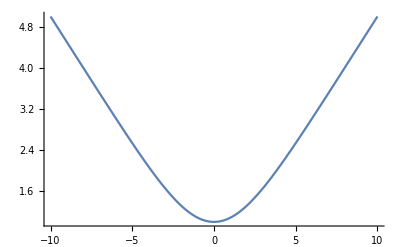

```mathematica
Plot[z/2*Coth[z/2],{z,-10,10}]
```

## Números de Bernoulli

```mathematica
BernoulliB[2]
```

1/6

```mathematica
Table[BernoulliB[k],{k,0,13}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66,0,-691/2730,0}

```mathematica
BernoulliB[-1]
```

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

BernoulliB[-1]

## Série de potências de ln[Γ(z+1)]

```mathematica
Series[Log[Gamma[z+1]],{z,0,6}]
```

-EulerGamma z+(π^2 z^2)/12+1/6 PolyGamma[2,1] z^3+(π^4 z^4)/360+1/120 PolyGamma[4,1] z^5+(π^6 z^6)/5670+O[z]^7

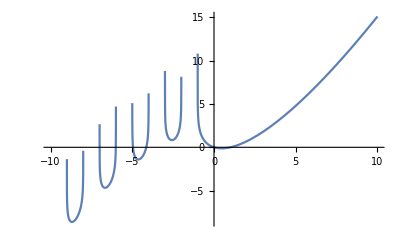

```mathematica
Plot[Log[Gamma[z+1]],{z,-10,10}]
```

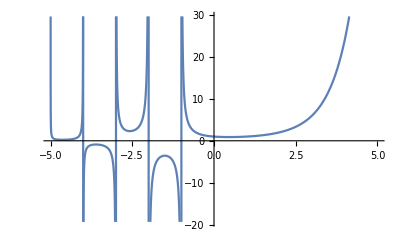

```mathematica
Plot[Gamma[z+1],{z,-5,5}]
```

## Expansão de Β(α,β+1) em torno de α = 0 e β = 0

```mathematica
A[α_,β_]:=Beta[α,β+1]
```

```mathematica
B[α_,β_]:=Series[Beta[α,β+1],{β,0,10}]
```

```mathematica
Beta[1/2,2+1]
```

16/15

```mathematica
Series[Beta[1/2,β+1],{β,0,10}]
```

2-2 (EulerGamma+PolyGamma[0,3/2]) β+1/3 (12+3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,3/2]+3 PolyGamma[0,3/2]^2) β^2+1/3 (-12 EulerGamma-EulerGamma^3+EulerGamma π^2-12 PolyGamma[0,3/2]-3 EulerGamma^2 PolyGamma[0,3/2]+π^2 PolyGamma[0,3/2]-3 EulerGamma PolyGamma[0,3/2]^2-PolyGamma[0,3/2]^3+PolyGamma[2,1]-PolyGamma[2,3/2]) β^3+1/60 (720+120 EulerGamma^2+5 EulerGamma^4-40 π^2-10 EulerGamma^2 π^2-3 π^4+240 EulerGamma PolyGamma[0,3/2]+20 EulerGamma^3 PolyGamma[0,3/2]-20 EulerGamma π^2 PolyGamma[0,3/2]+120 PolyGamma[0,3/2]^2+30 EulerGamma^2 PolyGamma[0,3/2]^2-10 π^2 PolyGamma[0,3/2]^2+20 EulerGamma PolyGamma[0,3/2]^3+5 PolyGamma[0,3/2]^4-20 EulerGamma PolyGamma[2,1]-20 PolyGamma[0,3/2] PolyGamma[2,1]+20 EulerGamma PolyGamma[2,3/2]+20 PolyGamma[0,3/2] PolyGamma[2,3/2]) β^4+1/180 (-2160 EulerGamma-120 EulerGamma^3-3 EulerGamma^5+120 EulerGamma π^2+10 EulerGamma^3 π^2+9 EulerGamma π^4-2160 PolyGamma[0,3/2]-360 EulerGamma^2 PolyGamma[0,3/2]-15 EulerGamma^4 PolyGamma[0,3/2]+120 π^2 PolyGamma[0,3/2]+30 EulerGamma^2 π^2 PolyGamma[0,3/2]+9 π^4 PolyGamma[0,3/2]-360 EulerGamma PolyGamma[0,3/2]^2-30 EulerGamma^3 PolyGamma[0,3/2]^2+30 EulerGamma π^2 PolyGamma[0,3/2]^2-120 PolyGamma[0,3/2]^3-30 EulerGamma^2 PolyGamma[0,3/2]^3+10 π^2 PolyGamma[0,3/2]^3-15 EulerGamma PolyGamma[0,3/2]^4-3 PolyGamma[0,3/2]^5+120 PolyGamma[2,1]+30 EulerGamma^2 PolyGamma[2,1]-10 π^2 PolyGamma[2,1]+60 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1]+30 PolyGamma[0,3/2]^2 PolyGamma[2,1]-120 PolyGamma[2,3/2]-30 EulerGamma^2 PolyGamma[2,3/2]+10 π^2 PolyGamma[2,3/2]-60 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2]-30 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+3 PolyGamma[4,1]-3 PolyGamma[4,3/2]) β^5+1/7560(302400+45360 EulerGamma^2+1260 EulerGamma^4+21 EulerGamma^6-15120 π^2-2520 EulerGamma^2 π^2-105 EulerGamma^4 π^2-756 π^4-189 EulerGamma^2 π^4-79 π^6+90720 EulerGamma PolyGamma[0,3/2]+5040 EulerGamma^3 PolyGamma[0,3/2]+126 EulerGamma^5 PolyGamma[0,3/2]-5040 EulerGamma π^2 PolyGamma[0,3/2]-420 EulerGamma^3 π^2 PolyGamma[0,3/2]-378 EulerGamma π^4 PolyGamma[0,3/2]+45360 PolyGamma[0,3/2]^2+7560 EulerGamma^2 PolyGamma[0,3/2]^2+315 EulerGamma^4 PolyGamma[0,3/2]^2-2520 π^2 PolyGamma[0,3/2]^2-630 EulerGamma^2 π^2 PolyGamma[0,3/2]^2-189 π^4 PolyGamma[0,3/2]^2+5040 EulerGamma PolyGamma[0,3/2]^3+420 EulerGamma^3 PolyGamma[0,3/2]^3-420 EulerGamma π^2 PolyGamma[0,3/2]^3+1260 PolyGamma[0,3/2]^4+315 EulerGamma^2 PolyGamma[0,3/2]^4-105 π^2 PolyGamma[0,3/2]^4+126 EulerGamma PolyGamma[0,3/2]^5+21 PolyGamma[0,3/2]^6-5040 EulerGamma PolyGamma[2,1]-420 EulerGamma^3 PolyGamma[2,1]+420 EulerGamma π^2 PolyGamma[2,1]-5040 PolyGamma[0,3/2] PolyGamma[2,1]-1260 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,1]+420 π^2 PolyGamma[0,3/2] PolyGamma[2,1]-1260 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,1]-420 PolyGamma[0,3/2]^3 PolyGamma[2,1]+210 PolyGamma[2,1]^2+5040 EulerGamma PolyGamma[2,3/2]+420 EulerGamma^3 PolyGamma[2,3/2]-420 EulerGamma π^2 PolyGamma[2,3/2]+5040 PolyGamma[0,3/2] PolyGamma[2,3/2]+1260 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-420 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]+1260 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+420 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-420 PolyGamma[2,1] PolyGamma[2,3/2]+210 PolyGamma[2,3/2]^2-126 EulerGamma PolyGamma[4,1]-126 PolyGamma[0,3/2] PolyGamma[4,1]+126 EulerGamma PolyGamma[4,3/2]+126 PolyGamma[0,3/2] PolyGamma[4,3/2]) β^6+1/7560(-302400 EulerGamma-15120 EulerGamma^3-252 EulerGamma^5-3 EulerGamma^7+15120 EulerGamma π^2+840 EulerGamma^3 π^2+21 EulerGamma^5 π^2+756 EulerGamma π^4+63 EulerGamma^3 π^4+79 EulerGamma π^6-302400 PolyGamma[0,3/2]-45360 EulerGamma^2 PolyGamma[0,3/2]-1260 EulerGamma^4 PolyGamma[0,3/2]-21 EulerGamma^6 PolyGamma[0,3/2]+15120 π^2 PolyGamma[0,3/2]+2520 EulerGamma^2 π^2 PolyGamma[0,3/2]+105 EulerGamma^4 π^2 PolyGamma[0,3/2]+756 π^4 PolyGamma[0,3/2]+189 EulerGamma^2 π^4 PolyGamma[0,3/2]+79 π^6 PolyGamma[0,3/2]-45360 EulerGamma PolyGamma[0,3/2]^2-2520 EulerGamma^3 PolyGamma[0,3/2]^2-63 EulerGamma^5 PolyGamma[0,3/2]^2+2520 EulerGamma π^2 PolyGamma[0,3/2]^2+210 EulerGamma^3 π^2 PolyGamma[0,3/2]^2+189 EulerGamma π^4 PolyGamma[0,3/2]^2-15120 PolyGamma[0,3/2]^3-2520 EulerGamma^2 PolyGamma[0,3/2]^3-105 EulerGamma^4 PolyGamma[0,3/2]^3+840 π^2 PolyGamma[0,3/2]^3+210 EulerGamma^2 π^2 PolyGamma[0,3/2]^3+63 π^4 PolyGamma[0,3/2]^3-1260 EulerGamma PolyGamma[0,3/2]^4-105 EulerGamma^3 PolyGamma[0,3/2]^4+105 EulerGamma π^2 PolyGamma[0,3/2]^4-252 PolyGamma[0,3/2]^5-63 EulerGamma^2 PolyGamma[0,3/2]^5+21 π^2 PolyGamma[0,3/2]^5-21 EulerGamma PolyGamma[0,3/2]^6-3 PolyGamma[0,3/2]^7+15120 PolyGamma[2,1]+2520 EulerGamma^2 PolyGamma[2,1]+105 EulerGamma^4 PolyGamma[2,1]-840 π^2 PolyGamma[2,1]-210 EulerGamma^2 π^2 PolyGamma[2,1]-63 π^4 PolyGamma[2,1]+5040 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1]+420 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,1]-420 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,1]+2520 PolyGamma[0,3/2]^2 PolyGamma[2,1]+630 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]-210 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]+420 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,1]+105 PolyGamma[0,3/2]^4 PolyGamma[2,1]-210 EulerGamma PolyGamma[2,1]^2-210 PolyGamma[0,3/2] PolyGamma[2,1]^2-15120 PolyGamma[2,3/2]-2520 EulerGamma^2 PolyGamma[2,3/2]-105 EulerGamma^4 PolyGamma[2,3/2]+840 π^2 PolyGamma[2,3/2]+210 EulerGamma^2 π^2 PolyGamma[2,3/2]+63 π^4 PolyGamma[2,3/2]-5040 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2]-420 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,3/2]+420 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-2520 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-630 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+210 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-420 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-105 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]+420 EulerGamma PolyGamma[2,1] PolyGamma[2,3/2]+420 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]-210 EulerGamma PolyGamma[2,3/2]^2-210 PolyGamma[0,3/2] PolyGamma[2,3/2]^2+252 PolyGamma[4,1]+63 EulerGamma^2 PolyGamma[4,1]-21 π^2 PolyGamma[4,1]+126 EulerGamma PolyGamma[0,3/2] PolyGamma[4,1]+63 PolyGamma[0,3/2]^2 PolyGamma[4,1]-252 PolyGamma[4,3/2]-63 EulerGamma^2 PolyGamma[4,3/2]+21 π^2 PolyGamma[4,3/2]-126 EulerGamma PolyGamma[0,3/2] PolyGamma[4,3/2]-63 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]+3 PolyGamma[6,1]-3 PolyGamma[6,3/2]) β^7+1/907200(127008000+18144000 EulerGamma^2+453600 EulerGamma^4+5040 EulerGamma^6+45 EulerGamma^8-6048000 π^2-907200 EulerGamma^2 π^2-25200 EulerGamma^4 π^2-420 EulerGamma^6 π^2-272160 π^4-45360 EulerGamma^2 π^4-1890 EulerGamma^4 π^4-18960 π^6-4740 EulerGamma^2 π^6-2339 π^8+36288000 EulerGamma PolyGamma[0,3/2]+1814400 EulerGamma^3 PolyGamma[0,3/2]+30240 EulerGamma^5 PolyGamma[0,3/2]+360 EulerGamma^7 PolyGamma[0,3/2]-1814400 EulerGamma π^2 PolyGamma[0,3/2]-100800 EulerGamma^3 π^2 PolyGamma[0,3/2]-2520 EulerGamma^5 π^2 PolyGamma[0,3/2]-90720 EulerGamma π^4 PolyGamma[0,3/2]-7560 EulerGamma^3 π^4 PolyGamma[0,3/2]-9480 EulerGamma π^6 PolyGamma[0,3/2]+18144000 PolyGamma[0,3/2]^2+2721600 EulerGamma^2 PolyGamma[0,3/2]^2+75600 EulerGamma^4 PolyGamma[0,3/2]^2+1260 EulerGamma^6 PolyGamma[0,3/2]^2-907200 π^2 PolyGamma[0,3/2]^2-151200 EulerGamma^2 π^2 PolyGamma[0,3/2]^2-6300 EulerGamma^4 π^2 PolyGamma[0,3/2]^2-45360 π^4 PolyGamma[0,3/2]^2-11340 EulerGamma^2 π^4 PolyGamma[0,3/2]^2-4740 π^6 PolyGamma[0,3/2]^2+1814400 EulerGamma PolyGamma[0,3/2]^3+100800 EulerGamma^3 PolyGamma[0,3/2]^3+2520 EulerGamma^5 PolyGamma[0,3/2]^3-100800 EulerGamma π^2 PolyGamma[0,3/2]^3-8400 EulerGamma^3 π^2 PolyGamma[0,3/2]^3-7560 EulerGamma π^4 PolyGamma[0,3/2]^3+453600 PolyGamma[0,3/2]^4+75600 EulerGamma^2 PolyGamma[0,3/2]^4+3150 EulerGamma^4 PolyGamma[0,3/2]^4-25200 π^2 PolyGamma[0,3/2]^4-6300 EulerGamma^2 π^2 PolyGamma[0,3/2]^4-1890 π^4 PolyGamma[0,3/2]^4+30240 EulerGamma PolyGamma[0,3/2]^5+2520 EulerGamma^3 PolyGamma[0,3/2]^5-2520 EulerGamma π^2 PolyGamma[0,3/2]^5+5040 PolyGamma[0,3/2]^6+1260 EulerGamma^2 PolyGamma[0,3/2]^6-420 π^2 PolyGamma[0,3/2]^6+360 EulerGamma PolyGamma[0,3/2]^7+45 PolyGamma[0,3/2]^8-1814400 EulerGamma PolyGamma[2,1]-100800 EulerGamma^3 PolyGamma[2,1]-2520 EulerGamma^5 PolyGamma[2,1]+100800 EulerGamma π^2 PolyGamma[2,1]+8400 EulerGamma^3 π^2 PolyGamma[2,1]+7560 EulerGamma π^4 PolyGamma[2,1]-1814400 PolyGamma[0,3/2] PolyGamma[2,1]-302400 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,1]-12600 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[2,1]+100800 π^2 PolyGamma[0,3/2] PolyGamma[2,1]+25200 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[2,1]+7560 π^4 PolyGamma[0,3/2] PolyGamma[2,1]-302400 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,1]-25200 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[2,1]+25200 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]-100800 PolyGamma[0,3/2]^3 PolyGamma[2,1]-25200 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]+8400 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]-12600 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[2,1]-2520 PolyGamma[0,3/2]^5 PolyGamma[2,1]+50400 PolyGamma[2,1]^2+12600 EulerGamma^2 PolyGamma[2,1]^2-4200 π^2 PolyGamma[2,1]^2+25200 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1]^2+12600 PolyGamma[0,3/2]^2 PolyGamma[2,1]^2+1814400 EulerGamma PolyGamma[2,3/2]+100800 EulerGamma^3 PolyGamma[2,3/2]+2520 EulerGamma^5 PolyGamma[2,3/2]-100800 EulerGamma π^2 PolyGamma[2,3/2]-8400 EulerGamma^3 π^2 PolyGamma[2,3/2]-7560 EulerGamma π^4 PolyGamma[2,3/2]+1814400 PolyGamma[0,3/2] PolyGamma[2,3/2]+302400 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,3/2]+12600 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[2,3/2]-100800 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-25200 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-7560 π^4 PolyGamma[0,3/2] PolyGamma[2,3/2]+302400 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+25200 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-25200 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+100800 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+25200 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-8400 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+12600 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[2,3/2]+2520 PolyGamma[0,3/2]^5 PolyGamma[2,3/2]-100800 PolyGamma[2,1] PolyGamma[2,3/2]-25200 EulerGamma^2 PolyGamma[2,1] PolyGamma[2,3/2]+8400 π^2 PolyGamma[2,1] PolyGamma[2,3/2]-50400 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]-25200 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[2,3/2]+50400 PolyGamma[2,3/2]^2+12600 EulerGamma^2 PolyGamma[2,3/2]^2-4200 π^2 PolyGamma[2,3/2]^2+25200 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2]^2+12600 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]^2-30240 EulerGamma PolyGamma[4,1]-2520 EulerGamma^3 PolyGamma[4,1]+2520 EulerGamma π^2 PolyGamma[4,1]-30240 PolyGamma[0,3/2] PolyGamma[4,1]-7560 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[4,1]+2520 π^2 PolyGamma[0,3/2] PolyGamma[4,1]-7560 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[4,1]-2520 PolyGamma[0,3/2]^3 PolyGamma[4,1]+2520 PolyGamma[2,1] PolyGamma[4,1]-2520 PolyGamma[2,3/2] PolyGamma[4,1]+30240 EulerGamma PolyGamma[4,3/2]+2520 EulerGamma^3 PolyGamma[4,3/2]-2520 EulerGamma π^2 PolyGamma[4,3/2]+30240 PolyGamma[0,3/2] PolyGamma[4,3/2]+7560 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[4,3/2]-2520 π^2 PolyGamma[0,3/2] PolyGamma[4,3/2]+7560 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[4,3/2]+2520 PolyGamma[0,3/2]^3 PolyGamma[4,3/2]-2520 PolyGamma[2,1] PolyGamma[4,3/2]+2520 PolyGamma[2,3/2] PolyGamma[4,3/2]-360 EulerGamma PolyGamma[6,1]-360 PolyGamma[0,3/2] PolyGamma[6,1]+360 EulerGamma PolyGamma[6,3/2]+360 PolyGamma[0,3/2] PolyGamma[6,3/2]) β^8+1/907200(-127008000 EulerGamma-6048000 EulerGamma^3-90720 EulerGamma^5-720 EulerGamma^7-5 EulerGamma^9+6048000 EulerGamma π^2+302400 EulerGamma^3 π^2+5040 EulerGamma^5 π^2+60 EulerGamma^7 π^2+272160 EulerGamma π^4+15120 EulerGamma^3 π^4+378 EulerGamma^5 π^4+18960 EulerGamma π^6+1580 EulerGamma^3 π^6+2339 EulerGamma π^8-127008000 PolyGamma[0,3/2]-18144000 EulerGamma^2 PolyGamma[0,3/2]-453600 EulerGamma^4 PolyGamma[0,3/2]-5040 EulerGamma^6 PolyGamma[0,3/2]-45 EulerGamma^8 PolyGamma[0,3/2]+6048000 π^2 PolyGamma[0,3/2]+907200 EulerGamma^2 π^2 PolyGamma[0,3/2]+25200 EulerGamma^4 π^2 PolyGamma[0,3/2]+420 EulerGamma^6 π^2 PolyGamma[0,3/2]+272160 π^4 PolyGamma[0,3/2]+45360 EulerGamma^2 π^4 PolyGamma[0,3/2]+1890 EulerGamma^4 π^4 PolyGamma[0,3/2]+18960 π^6 PolyGamma[0,3/2]+4740 EulerGamma^2 π^6 PolyGamma[0,3/2]+2339 π^8 PolyGamma[0,3/2]-18144000 EulerGamma PolyGamma[0,3/2]^2-907200 EulerGamma^3 PolyGamma[0,3/2]^2-15120 EulerGamma^5 PolyGamma[0,3/2]^2-180 EulerGamma^7 PolyGamma[0,3/2]^2+907200 EulerGamma π^2 PolyGamma[0,3/2]^2+50400 EulerGamma^3 π^2 PolyGamma[0,3/2]^2+1260 EulerGamma^5 π^2 PolyGamma[0,3/2]^2+45360 EulerGamma π^4 PolyGamma[0,3/2]^2+3780 EulerGamma^3 π^4 PolyGamma[0,3/2]^2+4740 EulerGamma π^6 PolyGamma[0,3/2]^2-6048000 PolyGamma[0,3/2]^3-907200 EulerGamma^2 PolyGamma[0,3/2]^3-25200 EulerGamma^4 PolyGamma[0,3/2]^3-420 EulerGamma^6 PolyGamma[0,3/2]^3+302400 π^2 PolyGamma[0,3/2]^3+50400 EulerGamma^2 π^2 PolyGamma[0,3/2]^3+2100 EulerGamma^4 π^2 PolyGamma[0,3/2]^3+15120 π^4 PolyGamma[0,3/2]^3+3780 EulerGamma^2 π^4 PolyGamma[0,3/2]^3+1580 π^6 PolyGamma[0,3/2]^3-453600 EulerGamma PolyGamma[0,3/2]^4-25200 EulerGamma^3 PolyGamma[0,3/2]^4-630 EulerGamma^5 PolyGamma[0,3/2]^4+25200 EulerGamma π^2 PolyGamma[0,3/2]^4+2100 EulerGamma^3 π^2 PolyGamma[0,3/2]^4+1890 EulerGamma π^4 PolyGamma[0,3/2]^4-90720 PolyGamma[0,3/2]^5-15120 EulerGamma^2 PolyGamma[0,3/2]^5-630 EulerGamma^4 PolyGamma[0,3/2]^5+5040 π^2 PolyGamma[0,3/2]^5+1260 EulerGamma^2 π^2 PolyGamma[0,3/2]^5+378 π^4 PolyGamma[0,3/2]^5-5040 EulerGamma PolyGamma[0,3/2]^6-420 EulerGamma^3 PolyGamma[0,3/2]^6+420 EulerGamma π^2 PolyGamma[0,3/2]^6-720 PolyGamma[0,3/2]^7-180 EulerGamma^2 PolyGamma[0,3/2]^7+60 π^2 PolyGamma[0,3/2]^7-45 EulerGamma PolyGamma[0,3/2]^8-5 PolyGamma[0,3/2]^9+6048000 PolyGamma[2,1]+907200 EulerGamma^2 PolyGamma[2,1]+25200 EulerGamma^4 PolyGamma[2,1]+420 EulerGamma^6 PolyGamma[2,1]-302400 π^2 PolyGamma[2,1]-50400 EulerGamma^2 π^2 PolyGamma[2,1]-2100 EulerGamma^4 π^2 PolyGamma[2,1]-15120 π^4 PolyGamma[2,1]-3780 EulerGamma^2 π^4 PolyGamma[2,1]-1580 π^6 PolyGamma[2,1]+1814400 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1]+100800 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,1]+2520 EulerGamma^5 PolyGamma[0,3/2] PolyGamma[2,1]-100800 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,1]-8400 EulerGamma^3 π^2 PolyGamma[0,3/2] PolyGamma[2,1]-7560 EulerGamma π^4 PolyGamma[0,3/2] PolyGamma[2,1]+907200 PolyGamma[0,3/2]^2 PolyGamma[2,1]+151200 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]+6300 EulerGamma^4 PolyGamma[0,3/2]^2 PolyGamma[2,1]-50400 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]-12600 EulerGamma^2 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]-3780 π^4 PolyGamma[0,3/2]^2 PolyGamma[2,1]+100800 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,1]+8400 EulerGamma^3 PolyGamma[0,3/2]^3 PolyGamma[2,1]-8400 EulerGamma π^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]+25200 PolyGamma[0,3/2]^4 PolyGamma[2,1]+6300 EulerGamma^2 PolyGamma[0,3/2]^4 PolyGamma[2,1]-2100 π^2 PolyGamma[0,3/2]^4 PolyGamma[2,1]+2520 EulerGamma PolyGamma[0,3/2]^5 PolyGamma[2,1]+420 PolyGamma[0,3/2]^6 PolyGamma[2,1]-50400 EulerGamma PolyGamma[2,1]^2-4200 EulerGamma^3 PolyGamma[2,1]^2+4200 EulerGamma π^2 PolyGamma[2,1]^2-50400 PolyGamma[0,3/2] PolyGamma[2,1]^2-12600 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,1]^2+4200 π^2 PolyGamma[0,3/2] PolyGamma[2,1]^2-12600 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,1]^2-4200 PolyGamma[0,3/2]^3 PolyGamma[2,1]^2+1400 PolyGamma[2,1]^3-6048000 PolyGamma[2,3/2]-907200 EulerGamma^2 PolyGamma[2,3/2]-25200 EulerGamma^4 PolyGamma[2,3/2]-420 EulerGamma^6 PolyGamma[2,3/2]+302400 π^2 PolyGamma[2,3/2]+50400 EulerGamma^2 π^2 PolyGamma[2,3/2]+2100 EulerGamma^4 π^2 PolyGamma[2,3/2]+15120 π^4 PolyGamma[2,3/2]+3780 EulerGamma^2 π^4 PolyGamma[2,3/2]+1580 π^6 PolyGamma[2,3/2]-1814400 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2]-100800 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,3/2]-2520 EulerGamma^5 PolyGamma[0,3/2] PolyGamma[2,3/2]+100800 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]+8400 EulerGamma^3 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]+7560 EulerGamma π^4 PolyGamma[0,3/2] PolyGamma[2,3/2]-907200 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-151200 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-6300 EulerGamma^4 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+50400 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+12600 EulerGamma^2 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+3780 π^4 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-100800 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-8400 EulerGamma^3 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+8400 EulerGamma π^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-25200 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]-6300 EulerGamma^2 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]+2100 π^2 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]-2520 EulerGamma PolyGamma[0,3/2]^5 PolyGamma[2,3/2]-420 PolyGamma[0,3/2]^6 PolyGamma[2,3/2]+100800 EulerGamma PolyGamma[2,1] PolyGamma[2,3/2]+8400 EulerGamma^3 PolyGamma[2,1] PolyGamma[2,3/2]-8400 EulerGamma π^2 PolyGamma[2,1] PolyGamma[2,3/2]+100800 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]+25200 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]-8400 π^2 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]+25200 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[2,3/2]+8400 PolyGamma[0,3/2]^3 PolyGamma[2,1] PolyGamma[2,3/2]-4200 PolyGamma[2,1]^2 PolyGamma[2,3/2]-50400 EulerGamma PolyGamma[2,3/2]^2-4200 EulerGamma^3 PolyGamma[2,3/2]^2+4200 EulerGamma π^2 PolyGamma[2,3/2]^2-50400 PolyGamma[0,3/2] PolyGamma[2,3/2]^2-12600 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,3/2]^2+4200 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]^2-12600 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,3/2]^2-4200 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]^2+4200 PolyGamma[2,1] PolyGamma[2,3/2]^2-1400 PolyGamma[2,3/2]^3+90720 PolyGamma[4,1]+15120 EulerGamma^2 PolyGamma[4,1]+630 EulerGamma^4 PolyGamma[4,1]-5040 π^2 PolyGamma[4,1]-1260 EulerGamma^2 π^2 PolyGamma[4,1]-378 π^4 PolyGamma[4,1]+30240 EulerGamma PolyGamma[0,3/2] PolyGamma[4,1]+2520 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[4,1]-2520 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[4,1]+15120 PolyGamma[0,3/2]^2 PolyGamma[4,1]+3780 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[4,1]-1260 π^2 PolyGamma[0,3/2]^2 PolyGamma[4,1]+2520 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[4,1]+630 PolyGamma[0,3/2]^4 PolyGamma[4,1]-2520 EulerGamma PolyGamma[2,1] PolyGamma[4,1]-2520 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[4,1]+2520 EulerGamma PolyGamma[2,3/2] PolyGamma[4,1]+2520 PolyGamma[0,3/2] PolyGamma[2,3/2] PolyGamma[4,1]-90720 PolyGamma[4,3/2]-15120 EulerGamma^2 PolyGamma[4,3/2]-630 EulerGamma^4 PolyGamma[4,3/2]+5040 π^2 PolyGamma[4,3/2]+1260 EulerGamma^2 π^2 PolyGamma[4,3/2]+378 π^4 PolyGamma[4,3/2]-30240 EulerGamma PolyGamma[0,3/2] PolyGamma[4,3/2]-2520 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[4,3/2]+2520 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[4,3/2]-15120 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]-3780 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]+1260 π^2 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]-2520 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[4,3/2]-630 PolyGamma[0,3/2]^4 PolyGamma[4,3/2]+2520 EulerGamma PolyGamma[2,1] PolyGamma[4,3/2]+2520 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[4,3/2]-2520 EulerGamma PolyGamma[2,3/2] PolyGamma[4,3/2]-2520 PolyGamma[0,3/2] PolyGamma[2,3/2] PolyGamma[4,3/2]+720 PolyGamma[6,1]+180 EulerGamma^2 PolyGamma[6,1]-60 π^2 PolyGamma[6,1]+360 EulerGamma PolyGamma[0,3/2] PolyGamma[6,1]+180 PolyGamma[0,3/2]^2 PolyGamma[6,1]-720 PolyGamma[6,3/2]-180 EulerGamma^2 PolyGamma[6,3/2]+60 π^2 PolyGamma[6,3/2]-360 EulerGamma PolyGamma[0,3/2] PolyGamma[6,3/2]-180 PolyGamma[0,3/2]^2 PolyGamma[6,3/2]+5 PolyGamma[8,1]-5 PolyGamma[8,3/2]) β^9+1/19958400(10059033600+1397088000 EulerGamma^2+33264000 EulerGamma^4+332640 EulerGamma^6+1980 EulerGamma^8+11 EulerGamma^10-465696000 π^2-66528000 EulerGamma^2 π^2-1663200 EulerGamma^4 π^2-18480 EulerGamma^6 π^2-165 EulerGamma^8 π^2-19958400 π^4-2993760 EulerGamma^2 π^4-83160 EulerGamma^4 π^4-1386 EulerGamma^6 π^4-1251360 π^6-208560 EulerGamma^2 π^6-8690 EulerGamma^4 π^6-102916 π^8-25729 EulerGamma^2 π^8-14217 π^10+2794176000 EulerGamma PolyGamma[0,3/2]+133056000 EulerGamma^3 PolyGamma[0,3/2]+1995840 EulerGamma^5 PolyGamma[0,3/2]+15840 EulerGamma^7 PolyGamma[0,3/2]+110 EulerGamma^9 PolyGamma[0,3/2]-133056000 EulerGamma π^2 PolyGamma[0,3/2]-6652800 EulerGamma^3 π^2 PolyGamma[0,3/2]-110880 EulerGamma^5 π^2 PolyGamma[0,3/2]-1320 EulerGamma^7 π^2 PolyGamma[0,3/2]-5987520 EulerGamma π^4 PolyGamma[0,3/2]-332640 EulerGamma^3 π^4 PolyGamma[0,3/2]-8316 EulerGamma^5 π^4 PolyGamma[0,3/2]-417120 EulerGamma π^6 PolyGamma[0,3/2]-34760 EulerGamma^3 π^6 PolyGamma[0,3/2]-51458 EulerGamma π^8 PolyGamma[0,3/2]+1397088000 PolyGamma[0,3/2]^2+199584000 EulerGamma^2 PolyGamma[0,3/2]^2+4989600 EulerGamma^4 PolyGamma[0,3/2]^2+55440 EulerGamma^6 PolyGamma[0,3/2]^2+495 EulerGamma^8 PolyGamma[0,3/2]^2-66528000 π^2 PolyGamma[0,3/2]^2-9979200 EulerGamma^2 π^2 PolyGamma[0,3/2]^2-277200 EulerGamma^4 π^2 PolyGamma[0,3/2]^2-4620 EulerGamma^6 π^2 PolyGamma[0,3/2]^2-2993760 π^4 PolyGamma[0,3/2]^2-498960 EulerGamma^2 π^4 PolyGamma[0,3/2]^2-20790 EulerGamma^4 π^4 PolyGamma[0,3/2]^2-208560 π^6 PolyGamma[0,3/2]^2-52140 EulerGamma^2 π^6 PolyGamma[0,3/2]^2-25729 π^8 PolyGamma[0,3/2]^2+133056000 EulerGamma PolyGamma[0,3/2]^3+6652800 EulerGamma^3 PolyGamma[0,3/2]^3+110880 EulerGamma^5 PolyGamma[0,3/2]^3+1320 EulerGamma^7 PolyGamma[0,3/2]^3-6652800 EulerGamma π^2 PolyGamma[0,3/2]^3-369600 EulerGamma^3 π^2 PolyGamma[0,3/2]^3-9240 EulerGamma^5 π^2 PolyGamma[0,3/2]^3-332640 EulerGamma π^4 PolyGamma[0,3/2]^3-27720 EulerGamma^3 π^4 PolyGamma[0,3/2]^3-34760 EulerGamma π^6 PolyGamma[0,3/2]^3+33264000 PolyGamma[0,3/2]^4+4989600 EulerGamma^2 PolyGamma[0,3/2]^4+138600 EulerGamma^4 PolyGamma[0,3/2]^4+2310 EulerGamma^6 PolyGamma[0,3/2]^4-1663200 π^2 PolyGamma[0,3/2]^4-277200 EulerGamma^2 π^2 PolyGamma[0,3/2]^4-11550 EulerGamma^4 π^2 PolyGamma[0,3/2]^4-83160 π^4 PolyGamma[0,3/2]^4-20790 EulerGamma^2 π^4 PolyGamma[0,3/2]^4-8690 π^6 PolyGamma[0,3/2]^4+1995840 EulerGamma PolyGamma[0,3/2]^5+110880 EulerGamma^3 PolyGamma[0,3/2]^5+2772 EulerGamma^5 PolyGamma[0,3/2]^5-110880 EulerGamma π^2 PolyGamma[0,3/2]^5-9240 EulerGamma^3 π^2 PolyGamma[0,3/2]^5-8316 EulerGamma π^4 PolyGamma[0,3/2]^5+332640 PolyGamma[0,3/2]^6+55440 EulerGamma^2 PolyGamma[0,3/2]^6+2310 EulerGamma^4 PolyGamma[0,3/2]^6-18480 π^2 PolyGamma[0,3/2]^6-4620 EulerGamma^2 π^2 PolyGamma[0,3/2]^6-1386 π^4 PolyGamma[0,3/2]^6+15840 EulerGamma PolyGamma[0,3/2]^7+1320 EulerGamma^3 PolyGamma[0,3/2]^7-1320 EulerGamma π^2 PolyGamma[0,3/2]^7+1980 PolyGamma[0,3/2]^8+495 EulerGamma^2 PolyGamma[0,3/2]^8-165 π^2 PolyGamma[0,3/2]^8+110 EulerGamma PolyGamma[0,3/2]^9+11 PolyGamma[0,3/2]^10-133056000 EulerGamma PolyGamma[2,1]-6652800 EulerGamma^3 PolyGamma[2,1]-110880 EulerGamma^5 PolyGamma[2,1]-1320 EulerGamma^7 PolyGamma[2,1]+6652800 EulerGamma π^2 PolyGamma[2,1]+369600 EulerGamma^3 π^2 PolyGamma[2,1]+9240 EulerGamma^5 π^2 PolyGamma[2,1]+332640 EulerGamma π^4 PolyGamma[2,1]+27720 EulerGamma^3 π^4 PolyGamma[2,1]+34760 EulerGamma π^6 PolyGamma[2,1]-133056000 PolyGamma[0,3/2] PolyGamma[2,1]-19958400 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,1]-554400 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[2,1]-9240 EulerGamma^6 PolyGamma[0,3/2] PolyGamma[2,1]+6652800 π^2 PolyGamma[0,3/2] PolyGamma[2,1]+1108800 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[2,1]+46200 EulerGamma^4 π^2 PolyGamma[0,3/2] PolyGamma[2,1]+332640 π^4 PolyGamma[0,3/2] PolyGamma[2,1]+83160 EulerGamma^2 π^4 PolyGamma[0,3/2] PolyGamma[2,1]+34760 π^6 PolyGamma[0,3/2] PolyGamma[2,1]-19958400 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,1]-1108800 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[2,1]-27720 EulerGamma^5 PolyGamma[0,3/2]^2 PolyGamma[2,1]+1108800 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]+92400 EulerGamma^3 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]+83160 EulerGamma π^4 PolyGamma[0,3/2]^2 PolyGamma[2,1]-6652800 PolyGamma[0,3/2]^3 PolyGamma[2,1]-1108800 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]-46200 EulerGamma^4 PolyGamma[0,3/2]^3 PolyGamma[2,1]+369600 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]+92400 EulerGamma^2 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,1]+27720 π^4 PolyGamma[0,3/2]^3 PolyGamma[2,1]-554400 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[2,1]-46200 EulerGamma^3 PolyGamma[0,3/2]^4 PolyGamma[2,1]+46200 EulerGamma π^2 PolyGamma[0,3/2]^4 PolyGamma[2,1]-110880 PolyGamma[0,3/2]^5 PolyGamma[2,1]-27720 EulerGamma^2 PolyGamma[0,3/2]^5 PolyGamma[2,1]+9240 π^2 PolyGamma[0,3/2]^5 PolyGamma[2,1]-9240 EulerGamma PolyGamma[0,3/2]^6 PolyGamma[2,1]-1320 PolyGamma[0,3/2]^7 PolyGamma[2,1]+3326400 PolyGamma[2,1]^2+554400 EulerGamma^2 PolyGamma[2,1]^2+23100 EulerGamma^4 PolyGamma[2,1]^2-184800 π^2 PolyGamma[2,1]^2-46200 EulerGamma^2 π^2 PolyGamma[2,1]^2-13860 π^4 PolyGamma[2,1]^2+1108800 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1]^2+92400 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,1]^2-92400 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,1]^2+554400 PolyGamma[0,3/2]^2 PolyGamma[2,1]^2+138600 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]^2-46200 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1]^2+92400 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,1]^2+23100 PolyGamma[0,3/2]^4 PolyGamma[2,1]^2-30800 EulerGamma PolyGamma[2,1]^3-30800 PolyGamma[0,3/2] PolyGamma[2,1]^3+133056000 EulerGamma PolyGamma[2,3/2]+6652800 EulerGamma^3 PolyGamma[2,3/2]+110880 EulerGamma^5 PolyGamma[2,3/2]+1320 EulerGamma^7 PolyGamma[2,3/2]-6652800 EulerGamma π^2 PolyGamma[2,3/2]-369600 EulerGamma^3 π^2 PolyGamma[2,3/2]-9240 EulerGamma^5 π^2 PolyGamma[2,3/2]-332640 EulerGamma π^4 PolyGamma[2,3/2]-27720 EulerGamma^3 π^4 PolyGamma[2,3/2]-34760 EulerGamma π^6 PolyGamma[2,3/2]+133056000 PolyGamma[0,3/2] PolyGamma[2,3/2]+19958400 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[2,3/2]+554400 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[2,3/2]+9240 EulerGamma^6 PolyGamma[0,3/2] PolyGamma[2,3/2]-6652800 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-1108800 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-46200 EulerGamma^4 π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]-332640 π^4 PolyGamma[0,3/2] PolyGamma[2,3/2]-83160 EulerGamma^2 π^4 PolyGamma[0,3/2] PolyGamma[2,3/2]-34760 π^6 PolyGamma[0,3/2] PolyGamma[2,3/2]+19958400 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+1108800 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+27720 EulerGamma^5 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-1108800 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-92400 EulerGamma^3 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]-83160 EulerGamma π^4 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]+6652800 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+1108800 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+46200 EulerGamma^4 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-369600 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-92400 EulerGamma^2 π^2 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]-27720 π^4 PolyGamma[0,3/2]^3 PolyGamma[2,3/2]+554400 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[2,3/2]+46200 EulerGamma^3 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]-46200 EulerGamma π^2 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]+110880 PolyGamma[0,3/2]^5 PolyGamma[2,3/2]+27720 EulerGamma^2 PolyGamma[0,3/2]^5 PolyGamma[2,3/2]-9240 π^2 PolyGamma[0,3/2]^5 PolyGamma[2,3/2]+9240 EulerGamma PolyGamma[0,3/2]^6 PolyGamma[2,3/2]+1320 PolyGamma[0,3/2]^7 PolyGamma[2,3/2]-6652800 PolyGamma[2,1] PolyGamma[2,3/2]-1108800 EulerGamma^2 PolyGamma[2,1] PolyGamma[2,3/2]-46200 EulerGamma^4 PolyGamma[2,1] PolyGamma[2,3/2]+369600 π^2 PolyGamma[2,1] PolyGamma[2,3/2]+92400 EulerGamma^2 π^2 PolyGamma[2,1] PolyGamma[2,3/2]+27720 π^4 PolyGamma[2,1] PolyGamma[2,3/2]-2217600 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]-184800 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]+184800 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]-1108800 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[2,3/2]-277200 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[2,3/2]+92400 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[2,3/2]-184800 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,1] PolyGamma[2,3/2]-46200 PolyGamma[0,3/2]^4 PolyGamma[2,1] PolyGamma[2,3/2]+92400 EulerGamma PolyGamma[2,1]^2 PolyGamma[2,3/2]+92400 PolyGamma[0,3/2] PolyGamma[2,1]^2 PolyGamma[2,3/2]+3326400 PolyGamma[2,3/2]^2+554400 EulerGamma^2 PolyGamma[2,3/2]^2+23100 EulerGamma^4 PolyGamma[2,3/2]^2-184800 π^2 PolyGamma[2,3/2]^2-46200 EulerGamma^2 π^2 PolyGamma[2,3/2]^2-13860 π^4 PolyGamma[2,3/2]^2+1108800 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2]^2+92400 EulerGamma^3 PolyGamma[0,3/2] PolyGamma[2,3/2]^2-92400 EulerGamma π^2 PolyGamma[0,3/2] PolyGamma[2,3/2]^2+554400 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]^2+138600 EulerGamma^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]^2-46200 π^2 PolyGamma[0,3/2]^2 PolyGamma[2,3/2]^2+92400 EulerGamma PolyGamma[0,3/2]^3 PolyGamma[2,3/2]^2+23100 PolyGamma[0,3/2]^4 PolyGamma[2,3/2]^2-92400 EulerGamma PolyGamma[2,1] PolyGamma[2,3/2]^2-92400 PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[2,3/2]^2+30800 EulerGamma PolyGamma[2,3/2]^3+30800 PolyGamma[0,3/2] PolyGamma[2,3/2]^3-1995840 EulerGamma PolyGamma[4,1]-110880 EulerGamma^3 PolyGamma[4,1]-2772 EulerGamma^5 PolyGamma[4,1]+110880 EulerGamma π^2 PolyGamma[4,1]+9240 EulerGamma^3 π^2 PolyGamma[4,1]+8316 EulerGamma π^4 PolyGamma[4,1]-1995840 PolyGamma[0,3/2] PolyGamma[4,1]-332640 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[4,1]-13860 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[4,1]+110880 π^2 PolyGamma[0,3/2] PolyGamma[4,1]+27720 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[4,1]+8316 π^4 PolyGamma[0,3/2] PolyGamma[4,1]-332640 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[4,1]-27720 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[4,1]+27720 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[4,1]-110880 PolyGamma[0,3/2]^3 PolyGamma[4,1]-27720 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[4,1]+9240 π^2 PolyGamma[0,3/2]^3 PolyGamma[4,1]-13860 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[4,1]-2772 PolyGamma[0,3/2]^5 PolyGamma[4,1]+110880 PolyGamma[2,1] PolyGamma[4,1]+27720 EulerGamma^2 PolyGamma[2,1] PolyGamma[4,1]-9240 π^2 PolyGamma[2,1] PolyGamma[4,1]+55440 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[4,1]+27720 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[4,1]-110880 PolyGamma[2,3/2] PolyGamma[4,1]-27720 EulerGamma^2 PolyGamma[2,3/2] PolyGamma[4,1]+9240 π^2 PolyGamma[2,3/2] PolyGamma[4,1]-55440 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2] PolyGamma[4,1]-27720 PolyGamma[0,3/2]^2 PolyGamma[2,3/2] PolyGamma[4,1]+1386 PolyGamma[4,1]^2+1995840 EulerGamma PolyGamma[4,3/2]+110880 EulerGamma^3 PolyGamma[4,3/2]+2772 EulerGamma^5 PolyGamma[4,3/2]-110880 EulerGamma π^2 PolyGamma[4,3/2]-9240 EulerGamma^3 π^2 PolyGamma[4,3/2]-8316 EulerGamma π^4 PolyGamma[4,3/2]+1995840 PolyGamma[0,3/2] PolyGamma[4,3/2]+332640 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[4,3/2]+13860 EulerGamma^4 PolyGamma[0,3/2] PolyGamma[4,3/2]-110880 π^2 PolyGamma[0,3/2] PolyGamma[4,3/2]-27720 EulerGamma^2 π^2 PolyGamma[0,3/2] PolyGamma[4,3/2]-8316 π^4 PolyGamma[0,3/2] PolyGamma[4,3/2]+332640 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[4,3/2]+27720 EulerGamma^3 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]-27720 EulerGamma π^2 PolyGamma[0,3/2]^2 PolyGamma[4,3/2]+110880 PolyGamma[0,3/2]^3 PolyGamma[4,3/2]+27720 EulerGamma^2 PolyGamma[0,3/2]^3 PolyGamma[4,3/2]-9240 π^2 PolyGamma[0,3/2]^3 PolyGamma[4,3/2]+13860 EulerGamma PolyGamma[0,3/2]^4 PolyGamma[4,3/2]+2772 PolyGamma[0,3/2]^5 PolyGamma[4,3/2]-110880 PolyGamma[2,1] PolyGamma[4,3/2]-27720 EulerGamma^2 PolyGamma[2,1] PolyGamma[4,3/2]+9240 π^2 PolyGamma[2,1] PolyGamma[4,3/2]-55440 EulerGamma PolyGamma[0,3/2] PolyGamma[2,1] PolyGamma[4,3/2]-27720 PolyGamma[0,3/2]^2 PolyGamma[2,1] PolyGamma[4,3/2]+110880 PolyGamma[2,3/2] PolyGamma[4,3/2]+27720 EulerGamma^2 PolyGamma[2,3/2] PolyGamma[4,3/2]-9240 π^2 PolyGamma[2,3/2] PolyGamma[4,3/2]+55440 EulerGamma PolyGamma[0,3/2] PolyGamma[2,3/2] PolyGamma[4,3/2]+27720 PolyGamma[0,3/2]^2 PolyGamma[2,3/2] PolyGamma[4,3/2]-2772 PolyGamma[4,1] PolyGamma[4,3/2]+1386 PolyGamma[4,3/2]^2-15840 EulerGamma PolyGamma[6,1]-1320 EulerGamma^3 PolyGamma[6,1]+1320 EulerGamma π^2 PolyGamma[6,1]-15840 PolyGamma[0,3/2] PolyGamma[6,1]-3960 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[6,1]+1320 π^2 PolyGamma[0,3/2] PolyGamma[6,1]-3960 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[6,1]-1320 PolyGamma[0,3/2]^3 PolyGamma[6,1]+1320 PolyGamma[2,1] PolyGamma[6,1]-1320 PolyGamma[2,3/2] PolyGamma[6,1]+15840 EulerGamma PolyGamma[6,3/2]+1320 EulerGamma^3 PolyGamma[6,3/2]-1320 EulerGamma π^2 PolyGamma[6,3/2]+15840 PolyGamma[0,3/2] PolyGamma[6,3/2]+3960 EulerGamma^2 PolyGamma[0,3/2] PolyGamma[6,3/2]-1320 π^2 PolyGamma[0,3/2] PolyGamma[6,3/2]+3960 EulerGamma PolyGamma[0,3/2]^2 PolyGamma[6,3/2]+1320 PolyGamma[0,3/2]^3 PolyGamma[6,3/2]-1320 PolyGamma[2,1] PolyGamma[6,3/2]+1320 PolyGamma[2,3/2] PolyGamma[6,3/2]-110 EulerGamma PolyGamma[8,1]-110 PolyGamma[0,3/2] PolyGamma[8,1]+110 EulerGamma PolyGamma[8,3/2]+110 PolyGamma[0,3/2] PolyGamma[8,3/2]) β^10+O[β]^11

```mathematica
C[B_]:=Series[B,{{α,0,10}}]
```

SetDelayed::write: Tag C in C[B_] is Protected.

$Failed

```mathematica
y[x_]:=x^2
```

```mathematica
y[2]
```

4

```mathematica
R=Series[Beta[α,β+1],{β,0,5}]
```

1/α-((EulerGamma+PolyGamma[0,1+α]) β)/α+1/(12 α)(6 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,1+α]+6 PolyGamma[0,1+α]^2-6 PolyGamma[1,1+α]) β^2-1/(12 α)(2 EulerGamma^3+EulerGamma π^2+6 EulerGamma^2 PolyGamma[0,1+α]+π^2 PolyGamma[0,1+α]+6 EulerGamma PolyGamma[0,1+α]^2+2 PolyGamma[0,1+α]^3-6 EulerGamma PolyGamma[1,1+α]-6 PolyGamma[0,1+α] PolyGamma[1,1+α]-2 PolyGamma[2,1]+2 PolyGamma[2,1+α]) β^3+1/(480 α)(20 EulerGamma^4+20 EulerGamma^2 π^2+3 π^4+80 EulerGamma^3 PolyGamma[0,1+α]+40 EulerGamma π^2 PolyGamma[0,1+α]+120 EulerGamma^2 PolyGamma[0,1+α]^2+20 π^2 PolyGamma[0,1+α]^2+80 EulerGamma PolyGamma[0,1+α]^3+20 PolyGamma[0,1+α]^4-120 EulerGamma^2 PolyGamma[1,1+α]-20 π^2 PolyGamma[1,1+α]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^2 PolyGamma[1,1+α]+60 PolyGamma[1,1+α]^2-80 EulerGamma PolyGamma[2,1]-80 PolyGamma[0,1+α] PolyGamma[2,1]+80 EulerGamma PolyGamma[2,1+α]+80 PolyGamma[0,1+α] PolyGamma[2,1+α]-20 PolyGamma[3,1+α]) β^4-1/(1440 α)(12 EulerGamma^5+20 EulerGamma^3 π^2+9 EulerGamma π^4+60 EulerGamma^4 PolyGamma[0,1+α]+60 EulerGamma^2 π^2 PolyGamma[0,1+α]+9 π^4 PolyGamma[0,1+α]+120 EulerGamma^3 PolyGamma[0,1+α]^2+60 EulerGamma π^2 PolyGamma[0,1+α]^2+120 EulerGamma^2 PolyGamma[0,1+α]^3+20 π^2 PolyGamma[0,1+α]^3+60 EulerGamma PolyGamma[0,1+α]^4+12 PolyGamma[0,1+α]^5-120 EulerGamma^3 PolyGamma[1,1+α]-60 EulerGamma π^2 PolyGamma[1,1+α]-360 EulerGamma^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-60 π^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-360 EulerGamma PolyGamma[0,1+α]^2 PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^3 PolyGamma[1,1+α]+180 EulerGamma PolyGamma[1,1+α]^2+180 PolyGamma[0,1+α] PolyGamma[1,1+α]^2-120 EulerGamma^2 PolyGamma[2,1]-20 π^2 PolyGamma[2,1]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1]-120 PolyGamma[0,1+α]^2 PolyGamma[2,1]+120 PolyGamma[1,1+α] PolyGamma[2,1]+120 EulerGamma^2 PolyGamma[2,1+α]+20 π^2 PolyGamma[2,1+α]+240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1+α]+120 PolyGamma[0,1+α]^2 PolyGamma[2,1+α]-120 PolyGamma[1,1+α] PolyGamma[2,1+α]-60 EulerGamma PolyGamma[3,1+α]-60 PolyGamma[0,1+α] PolyGamma[3,1+α]-12 PolyGamma[4,1]+12 PolyGamma[4,1+α]) β^5+O[β]^6

```mathematica
R1=1/α-((EulerGamma+PolyGamma[0,1+α]) β)/α+1/(12 α)(6 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,1+α]+6 PolyGamma[0,1+α]^2-6 PolyGamma[1,1+α]) β^2-1/(12 α)(2 EulerGamma^3+EulerGamma π^2+6 EulerGamma^2 PolyGamma[0,1+α]+π^2 PolyGamma[0,1+α]+6 EulerGamma PolyGamma[0,1+α]^2+2 PolyGamma[0,1+α]^3-6 EulerGamma PolyGamma[1,1+α]-6 PolyGamma[0,1+α] PolyGamma[1,1+α]-2 PolyGamma[2,1]+2 PolyGamma[2,1+α]) β^3+1/(480 α)(20 EulerGamma^4+20 EulerGamma^2 π^2+3 π^4+80 EulerGamma^3 PolyGamma[0,1+α]+40 EulerGamma π^2 PolyGamma[0,1+α]+120 EulerGamma^2 PolyGamma[0,1+α]^2+20 π^2 PolyGamma[0,1+α]^2+80 EulerGamma PolyGamma[0,1+α]^3+20 PolyGamma[0,1+α]^4-120 EulerGamma^2 PolyGamma[1,1+α]-20 π^2 PolyGamma[1,1+α]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^2 PolyGamma[1,1+α]+60 PolyGamma[1,1+α]^2-80 EulerGamma PolyGamma[2,1]-80 PolyGamma[0,1+α] PolyGamma[2,1]+80 EulerGamma PolyGamma[2,1+α]+80 PolyGamma[0,1+α] PolyGamma[2,1+α]-20 PolyGamma[3,1+α]) β^4-1/(1440 α)(12 EulerGamma^5+20 EulerGamma^3 π^2+9 EulerGamma π^4+60 EulerGamma^4 PolyGamma[0,1+α]+60 EulerGamma^2 π^2 PolyGamma[0,1+α]+9 π^4 PolyGamma[0,1+α]+120 EulerGamma^3 PolyGamma[0,1+α]^2+60 EulerGamma π^2 PolyGamma[0,1+α]^2+120 EulerGamma^2 PolyGamma[0,1+α]^3+20 π^2 PolyGamma[0,1+α]^3+60 EulerGamma PolyGamma[0,1+α]^4+12 PolyGamma[0,1+α]^5-120 EulerGamma^3 PolyGamma[1,1+α]-60 EulerGamma π^2 PolyGamma[1,1+α]-360 EulerGamma^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-60 π^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-360 EulerGamma PolyGamma[0,1+α]^2 PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^3 PolyGamma[1,1+α]+180 EulerGamma PolyGamma[1,1+α]^2+180 PolyGamma[0,1+α] PolyGamma[1,1+α]^2-120 EulerGamma^2 PolyGamma[2,1]-20 π^2 PolyGamma[2,1]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1]-120 PolyGamma[0,1+α]^2 PolyGamma[2,1]+120 PolyGamma[1,1+α] PolyGamma[2,1]+120 EulerGamma^2 PolyGamma[2,1+α]+20 π^2 PolyGamma[2,1+α]+240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1+α]+120 PolyGamma[0,1+α]^2 PolyGamma[2,1+α]-120 PolyGamma[1,1+α] PolyGamma[2,1+α]-60 EulerGamma PolyGamma[3,1+α]-60 PolyGamma[0,1+α] PolyGamma[3,1+α]-12 PolyGamma[4,1]+12 PolyGamma[4,1+α]) β^5
```

1/α-(β (EulerGamma+PolyGamma[0,1+α]))/α+1/(12 α)β^2 (6 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,1+α]+6 PolyGamma[0,1+α]^2-6 PolyGamma[1,1+α])-1/(12 α)β^3 (2 EulerGamma^3+EulerGamma π^2+6 EulerGamma^2 PolyGamma[0,1+α]+π^2 PolyGamma[0,1+α]+6 EulerGamma PolyGamma[0,1+α]^2+2 PolyGamma[0,1+α]^3-6 EulerGamma PolyGamma[1,1+α]-6 PolyGamma[0,1+α] PolyGamma[1,1+α]-2 PolyGamma[2,1]+2 PolyGamma[2,1+α])+1/(480 α)β^4 (20 EulerGamma^4+20 EulerGamma^2 π^2+3 π^4+80 EulerGamma^3 PolyGamma[0,1+α]+40 EulerGamma π^2 PolyGamma[0,1+α]+120 EulerGamma^2 PolyGamma[0,1+α]^2+20 π^2 PolyGamma[0,1+α]^2+80 EulerGamma PolyGamma[0,1+α]^3+20 PolyGamma[0,1+α]^4-120 EulerGamma^2 PolyGamma[1,1+α]-20 π^2 PolyGamma[1,1+α]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^2 PolyGamma[1,1+α]+60 PolyGamma[1,1+α]^2-80 EulerGamma PolyGamma[2,1]-80 PolyGamma[0,1+α] PolyGamma[2,1]+80 EulerGamma PolyGamma[2,1+α]+80 PolyGamma[0,1+α] PolyGamma[2,1+α]-20 PolyGamma[3,1+α])-1/(1440 α)β^5 (12 EulerGamma^5+20 EulerGamma^3 π^2+9 EulerGamma π^4+60 EulerGamma^4 PolyGamma[0,1+α]+60 EulerGamma^2 π^2 PolyGamma[0,1+α]+9 π^4 PolyGamma[0,1+α]+120 EulerGamma^3 PolyGamma[0,1+α]^2+60 EulerGamma π^2 PolyGamma[0,1+α]^2+120 EulerGamma^2 PolyGamma[0,1+α]^3+20 π^2 PolyGamma[0,1+α]^3+60 EulerGamma PolyGamma[0,1+α]^4+12 PolyGamma[0,1+α]^5-120 EulerGamma^3 PolyGamma[1,1+α]-60 EulerGamma π^2 PolyGamma[1,1+α]-360 EulerGamma^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-60 π^2 PolyGamma[0,1+α] PolyGamma[1,1+α]-360 EulerGamma PolyGamma[0,1+α]^2 PolyGamma[1,1+α]-120 PolyGamma[0,1+α]^3 PolyGamma[1,1+α]+180 EulerGamma PolyGamma[1,1+α]^2+180 PolyGamma[0,1+α] PolyGamma[1,1+α]^2-120 EulerGamma^2 PolyGamma[2,1]-20 π^2 PolyGamma[2,1]-240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1]-120 PolyGamma[0,1+α]^2 PolyGamma[2,1]+120 PolyGamma[1,1+α] PolyGamma[2,1]+120 EulerGamma^2 PolyGamma[2,1+α]+20 π^2 PolyGamma[2,1+α]+240 EulerGamma PolyGamma[0,1+α] PolyGamma[2,1+α]+120 PolyGamma[0,1+α]^2 PolyGamma[2,1+α]-120 PolyGamma[1,1+α] PolyGamma[2,1+α]-60 EulerGamma PolyGamma[3,1+α]-60 PolyGamma[0,1+α] PolyGamma[3,1+α]-12 PolyGamma[4,1]+12 PolyGamma[4,1+α])

```mathematica
S=Series[R1,{α,0,5}]
```

1/α+(-1260 π^2 β-84 π^4 β^3-8 π^6 β^5-3780 β^2 PolyGamma[2,1]-315 β^4 PolyGamma[4,1])/7560+1/5040(-14 π^4 β^2-4 π^6 β^4-2520 β PolyGamma[2,1]+420 π^2 β^3 PolyGamma[2,1]+28 π^4 β^5 PolyGamma[2,1]+630 β^4 PolyGamma[2,1]^2-420 β^3 PolyGamma[4,1]+35 π^2 β^5 PolyGamma[4,1]-21 β^5 PolyGamma[6,1]) α+1/226800(-2520 π^4 β-345 π^6 β^3-61 π^8 β^5+18900 π^2 β^2 PolyGamma[2,1]+1575 π^4 β^4 PolyGamma[2,1]+56700 β^3 PolyGamma[2,1]^2-4725 π^2 β^5 PolyGamma[2,1]^2-18900 β^2 PolyGamma[4,1]+3150 π^2 β^4 PolyGamma[4,1]+14175 β^5 PolyGamma[2,1] PolyGamma[4,1]-1575 β^4 PolyGamma[6,1]) α^2+(-(π^6 β^2)/1260+1/8 β^2 PolyGamma[2,1]^2-1/24 β PolyGamma[4,1]+(β^4 (-499 π^8-75600 π^2 PolyGamma[2,1]^2+151200 PolyGamma[2,1] PolyGamma[4,1]))/1814400+1/144 (π^4 β^3 PolyGamma[2,1]+2 π^2 β^3 PolyGamma[4,1]-β^3 PolyGamma[6,1])+1/8640 β^5 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1])) α^3+(-(π^6 β)/945+(-61 π^8 β^3-4725 π^2 β^3 PolyGamma[2,1]^2+14175 β^3 PolyGamma[2,1] PolyGamma[4,1])/226800+1/720 (4 π^4 β^2 PolyGamma[2,1]+5 π^2 β^2 PolyGamma[4,1]-3 β^2 PolyGamma[6,1])+1/1900800 β^5 (-149 π^10-6600 π^4 PolyGamma[2,1]^2-26400 π^2 PolyGamma[2,1] PolyGamma[4,1]+16500 PolyGamma[4,1]^2+13200 PolyGamma[2,1] PolyGamma[6,1])+1/8640 β^4 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1])) α^4+(-(π^8 β^2)/7560+1/48 β^2 PolyGamma[2,1] PolyGamma[4,1]-1/720 β PolyGamma[6,1]+1/4276800 β^4 (-278 π^10-13365 π^4 PolyGamma[2,1]^2-44550 π^2 PolyGamma[2,1] PolyGamma[4,1]+29700 PolyGamma[4,1]^2+23760 PolyGamma[2,1] PolyGamma[6,1])+1/8640(8 π^6 β^3 PolyGamma[2,1]-180 β^3 PolyGamma[2,1]^3+9 π^4 β^3 PolyGamma[4,1]+6 π^2 β^3 PolyGamma[6,1]-2 β^3 PolyGamma[8,1])+1/518400 β^5 (141 π^8 PolyGamma[2,1]+5400 π^2 PolyGamma[2,1]^3+140 π^6 PolyGamma[4,1]-18900 PolyGamma[2,1]^2 PolyGamma[4,1]+74 π^4 PolyGamma[6,1]+30 π^2 PolyGamma[8,1]-6 PolyGamma[10,1])) α^5+O[α]^6

```mathematica
S1=1/α+(-1260 π^2 β-84 π^4 β^3-8 π^6 β^5-3780 β^2 PolyGamma[2,1]-315 β^4 PolyGamma[4,1])/7560+1/5040(-14 π^4 β^2-4 π^6 β^4-2520 β PolyGamma[2,1]+420 π^2 β^3 PolyGamma[2,1]+28 π^4 β^5 PolyGamma[2,1]+630 β^4 PolyGamma[2,1]^2-420 β^3 PolyGamma[4,1]+35 π^2 β^5 PolyGamma[4,1]-21 β^5 PolyGamma[6,1]) α+1/226800(-2520 π^4 β-345 π^6 β^3-61 π^8 β^5+18900 π^2 β^2 PolyGamma[2,1]+1575 π^4 β^4 PolyGamma[2,1]+56700 β^3 PolyGamma[2,1]^2-4725 π^2 β^5 PolyGamma[2,1]^2-18900 β^2 PolyGamma[4,1]+3150 π^2 β^4 PolyGamma[4,1]+14175 β^5 PolyGamma[2,1] PolyGamma[4,1]-1575 β^4 PolyGamma[6,1]) α^2+(-(π^6 β^2)/1260+1/8 β^2 PolyGamma[2,1]^2-1/24 β PolyGamma[4,1]+(β^4 (-499 π^8-75600 π^2 PolyGamma[2,1]^2+151200 PolyGamma[2,1] PolyGamma[4,1]))/1814400+1/144 (π^4 β^3 PolyGamma[2,1]+2 π^2 β^3 PolyGamma[4,1]-β^3 PolyGamma[6,1])+1/8640 β^5 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1])) α^3+(-(π^6 β)/945+(-61 π^8 β^3-4725 π^2 β^3 PolyGamma[2,1]^2+14175 β^3 PolyGamma[2,1] PolyGamma[4,1])/226800+1/720 (4 π^4 β^2 PolyGamma[2,1]+5 π^2 β^2 PolyGamma[4,1]-3 β^2 PolyGamma[6,1])+1/1900800 β^5 (-149 π^10-6600 π^4 PolyGamma[2,1]^2-26400 π^2 PolyGamma[2,1] PolyGamma[4,1]+16500 PolyGamma[4,1]^2+13200 PolyGamma[2,1] PolyGamma[6,1])+1/8640 β^4 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1])) α^4+(-(π^8 β^2)/7560+1/48 β^2 PolyGamma[2,1] PolyGamma[4,1]-1/720 β PolyGamma[6,1]+1/4276800 β^4 (-278 π^10-13365 π^4 PolyGamma[2,1]^2-44550 π^2 PolyGamma[2,1] PolyGamma[4,1]+29700 PolyGamma[4,1]^2+23760 PolyGamma[2,1] PolyGamma[6,1])+1/8640(8 π^6 β^3 PolyGamma[2,1]-180 β^3 PolyGamma[2,1]^3+9 π^4 β^3 PolyGamma[4,1]+6 π^2 β^3 PolyGamma[6,1]-2 β^3 PolyGamma[8,1])+1/518400 β^5 (141 π^8 PolyGamma[2,1]+5400 π^2 PolyGamma[2,1]^3+140 π^6 PolyGamma[4,1]-18900 PolyGamma[2,1]^2 PolyGamma[4,1]+74 π^4 PolyGamma[6,1]+30 π^2 PolyGamma[8,1]-6 PolyGamma[10,1])) α^5
```

1/α+(-1260 π^2 β-84 π^4 β^3-8 π^6 β^5-3780 β^2 PolyGamma[2,1]-315 β^4 PolyGamma[4,1])/7560+1/226800 α^2 (-2520 π^4 β-345 π^6 β^3-61 π^8 β^5+18900 π^2 β^2 PolyGamma[2,1]+1575 π^4 β^4 PolyGamma[2,1]+56700 β^3 PolyGamma[2,1]^2-4725 π^2 β^5 PolyGamma[2,1]^2-18900 β^2 PolyGamma[4,1]+3150 π^2 β^4 PolyGamma[4,1]+14175 β^5 PolyGamma[2,1] PolyGamma[4,1]-1575 β^4 PolyGamma[6,1])+1/5040 α (-14 π^4 β^2-4 π^6 β^4-2520 β PolyGamma[2,1]+420 π^2 β^3 PolyGamma[2,1]+28 π^4 β^5 PolyGamma[2,1]+630 β^4 PolyGamma[2,1]^2-420 β^3 PolyGamma[4,1]+35 π^2 β^5 PolyGamma[4,1]-21 β^5 PolyGamma[6,1])+α^4 (-(π^6 β)/945+(-61 π^8 β^3-4725 π^2 β^3 PolyGamma[2,1]^2+14175 β^3 PolyGamma[2,1] PolyGamma[4,1])/226800+1/720 (4 π^4 β^2 PolyGamma[2,1]+5 π^2 β^2 PolyGamma[4,1]-3 β^2 PolyGamma[6,1])+1/1900800 β^5 (-149 π^10-6600 π^4 PolyGamma[2,1]^2-26400 π^2 PolyGamma[2,1] PolyGamma[4,1]+16500 PolyGamma[4,1]^2+13200 PolyGamma[2,1] PolyGamma[6,1])+1/8640 β^4 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1]))+α^3 (-(π^6 β^2)/1260+1/8 β^2 PolyGamma[2,1]^2-1/24 β PolyGamma[4,1]+(β^4 (-499 π^8-75600 π^2 PolyGamma[2,1]^2+151200 PolyGamma[2,1] PolyGamma[4,1]))/1814400+1/144 (π^4 β^3 PolyGamma[2,1]+2 π^2 β^3 PolyGamma[4,1]-β^3 PolyGamma[6,1])+1/8640 β^5 (10 π^6 PolyGamma[2,1]-540 PolyGamma[2,1]^3+14 π^4 PolyGamma[4,1]+10 π^2 PolyGamma[6,1]-3 PolyGamma[8,1]))+α^5 (-(π^8 β^2)/7560+1/48 β^2 PolyGamma[2,1] PolyGamma[4,1]-1/720 β PolyGamma[6,1]+1/4276800 β^4 (-278 π^10-13365 π^4 PolyGamma[2,1]^2-44550 π^2 PolyGamma[2,1] PolyGamma[4,1]+29700 PolyGamma[4,1]^2+23760 PolyGamma[2,1] PolyGamma[6,1])+1/8640(8 π^6 β^3 PolyGamma[2,1]-180 β^3 PolyGamma[2,1]^3+9 π^4 β^3 PolyGamma[4,1]+6 π^2 β^3 PolyGamma[6,1]-2 β^3 PolyGamma[8,1])+1/518400 β^5 (141 π^8 PolyGamma[2,1]+5400 π^2 PolyGamma[2,1]^3+140 π^6 PolyGamma[4,1]-18900 PolyGamma[2,1]^2 PolyGamma[4,1]+74 π^4 PolyGamma[6,1]+30 π^2 PolyGamma[8,1]-6 PolyGamma[10,1]))

```mathematica
S2=Expand[S1]
```

1/α-(π^2 β)/6-1/90 π^4 α^2 β-1/945 π^6 α^4 β-1/360 π^4 α β^2-(π^6 α^3 β^2)/1260-(π^8 α^5 β^2)/7560-(π^4 β^3)/90-(23 π^6 α^2 β^3)/15120-(61 π^8 α^4 β^3)/226800-(π^6 α β^4)/1260-(499 π^8 α^3 β^4)/1814400-(139 π^10 α^5 β^4)/2138400-(π^6 β^5)/945-(61 π^8 α^2 β^5)/226800-(149 π^10 α^4 β^5)/1900800-1/2 α β PolyGamma[2,1]-1/2 β^2 PolyGamma[2,1]+1/12 π^2 α^2 β^2 PolyGamma[2,1]+1/180 π^4 α^4 β^2 PolyGamma[2,1]+1/12 π^2 α β^3 PolyGamma[2,1]+1/144 π^4 α^3 β^3 PolyGamma[2,1]+(π^6 α^5 β^3 PolyGamma[2,1])/1080+1/144 π^4 α^2 β^4 PolyGamma[2,1]+1/864 π^6 α^4 β^4 PolyGamma[2,1]+1/180 π^4 α β^5 PolyGamma[2,1]+1/864 π^6 α^3 β^5 PolyGamma[2,1]+(47 π^8 α^5 β^5 PolyGamma[2,1])/172800+1/8 α^3 β^2 PolyGamma[2,1]^2+1/4 α^2 β^3 PolyGamma[2,1]^2-1/48 π^2 α^4 β^3 PolyGamma[2,1]^2+1/8 α β^4 PolyGamma[2,1]^2-1/24 π^2 α^3 β^4 PolyGamma[2,1]^2-1/320 π^4 α^5 β^4 PolyGamma[2,1]^2-1/48 π^2 α^2 β^5 PolyGamma[2,1]^2-1/288 π^4 α^4 β^5 PolyGamma[2,1]^2-1/48 α^5 β^3 PolyGamma[2,1]^3-1/16 α^4 β^4 PolyGamma[2,1]^3-1/16 α^3 β^5 PolyGamma[2,1]^3+1/96 π^2 α^5 β^5 PolyGamma[2,1]^3-1/24 α^3 β PolyGamma[4,1]-1/12 α^2 β^2 PolyGamma[4,1]+1/144 π^2 α^4 β^2 PolyGamma[4,1]-1/12 α β^3 PolyGamma[4,1]+1/72 π^2 α^3 β^3 PolyGamma[4,1]+1/960 π^4 α^5 β^3 PolyGamma[4,1]-1/24 β^4 PolyGamma[4,1]+1/72 π^2 α^2 β^4 PolyGamma[4,1]+(7 π^4 α^4 β^4 PolyGamma[4,1])/4320+1/144 π^2 α β^5 PolyGamma[4,1]+(7 π^4 α^3 β^5 PolyGamma[4,1])/4320+(7 π^6 α^5 β^5 PolyGamma[4,1])/25920+1/48 α^5 β^2 PolyGamma[2,1] PolyGamma[4,1]+1/16 α^4 β^3 PolyGamma[2,1] PolyGamma[4,1]+1/12 α^3 β^4 PolyGamma[2,1] PolyGamma[4,1]-1/96 π^2 α^5 β^4 PolyGamma[2,1] PolyGamma[4,1]+1/16 α^2 β^5 PolyGamma[2,1] PolyGamma[4,1]-1/72 π^2 α^4 β^5 PolyGamma[2,1] PolyGamma[4,1]-7/192 α^5 β^5 PolyGamma[2,1]^2 PolyGamma[4,1]+1/144 α^5 β^4 PolyGamma[4,1]^2+5/576 α^4 β^5 PolyGamma[4,1]^2-1/720 α^5 β PolyGamma[6,1]-1/240 α^4 β^2 PolyGamma[6,1]-1/144 α^3 β^3 PolyGamma[6,1]+(π^2 α^5 β^3 PolyGamma[6,1])/1440-1/144 α^2 β^4 PolyGamma[6,1]+1/864 π^2 α^4 β^4 PolyGamma[6,1]-1/240 α β^5 PolyGamma[6,1]+1/864 π^2 α^3 β^5 PolyGamma[6,1]+(37 π^4 α^5 β^5 PolyGamma[6,1])/259200+1/180 α^5 β^4 PolyGamma[2,1] PolyGamma[6,1]+1/144 α^4 β^5 PolyGamma[2,1] PolyGamma[6,1]-(α^5 β^3 PolyGamma[8,1])/4320-(α^4 β^4 PolyGamma[8,1])/2880-(α^3 β^5 PolyGamma[8,1])/2880+(π^2 α^5 β^5 PolyGamma[8,1])/17280-(α^5 β^5 PolyGamma[10,1])/86400

```mathematica
C1=Coefficient[Coefficient[S2,α^2],β^2]
```

1/12 π^2 PolyGamma[2,1]-1/12 PolyGamma[4,1]

```mathematica
FullSimplify[C1]
```

-1/6 π^2 Zeta[3]+2 Zeta[5]

```mathematica
Sum[p,{p,N}]
```

1/2 N (1+N)

```mathematica
Sum[Sum[1/(n^2*p),{p,n}],{n,5}]
```

388853/216000

```mathematica
M=0
```

0

```mathematica
Do[M=M+p,{p,1,5}]
```

```mathematica
M
```

15

```mathematica
M=0
```

0

```mathematica
Do[Do[M=M+1/(n^2*p),{p,1,n}],{n,1,5}]
```

```mathematica
M
```

388853/216000

```mathematica
C[m,p]=Coefficient[Coefficient[S2,α^m],β^p]
```

Set::write: Tag C in C[m, p] is Protected.

0

```mathematica
Do[Do[c[m,p]=FullSimplify[Coefficient[Coefficient[S2,α^m],β^p]],{p,1,5}],{m,1,5}]
```

```mathematica
c[1,2]
```

-π^4/360

```mathematica
c[2,3]
```

-(23 π^6)/15120+Zeta[3]^2